# John Horton Conway: The Game of Life and Disease Modelling (Logbook)

## Conway’s Game of Life

This is a demonstration of how Conway’s Game of Life model actually works. As mentioned, there are two parts to the model:

1. An initial array. This consists of lots of cells labelled as ‘0’ (dead) or ‘1’ (alive). In this case, I have spent a very long time getting the initial array to spell ‘KINESIS’
2. A set of rules. Here, I have captured the rules of ‘Life’ into two rules:
	- ruleDead: Take a cell labelled ‘0’ and sum the surrounding cells. If the sum is equal to 3, the cell is converted to ‘1’. If not, we leave it as ‘0’.
	- ruleAlive: Take a cell labelled ‘1’ and sum the surrounding cells. If the sum is equal to 2 or 3, the cell stays as ‘1’. If not, it is converted to ‘0’.
	
Finally, the initial array and rules are combined into an update function, updLife, which runs the model for 100 iterations.

```mathematica
dimi = 11;
dimj = 30;
(* Initial Array *)
init = Table[0, {dimi}, {dimj}];
(* K *)
init[[{4,5,6,7,8},4]] = {1,1,1,1,1};
init[[{5,6},5]] = {1,1};
init[[{4,7,8},6]] = {1,1,1};
(* I *)
init[[{4,5,6,7,8},8]] = {1,1,1,1,1};
(* N *)
init[[{4,5,6,7,8},10]] = {1,1,1,1,1};
init[[5,11]] = 1;
init[[6,12]] = 1;
init[[{4,5,6,7,8},13]] = {1,1,1,1,1};
(* E *)
init[[{4,5,6,7,8},15]] = {1,1,1,1,1};
init[[{4,6,8},16]] = {1,1,1};
init[[{4,6,8},17]] = {1,1,1};
(* S *)
init[[{4,5,6,8},19]] = {1,1,1,1};
init[[{4,6,8},20]] = {1,1,1};
init[[{4,6,7,8},21]] = {1,1,1,1};
(* I *)
init[[{4,5,6,7,8},23]] = {1,1,1,1,1};
(* S *)
init[[{4,5,6,8},25]] = {1,1,1,1};
init[[{4,6,8},26]] = {1,1,1};
init[[{4,6,7,8},27]] = {1,1,1,1};

ArrayPlot[init]
```

-Graphics-

```mathematica
ruleDead = {{a1_,b1_,c1_},{a2_,0,c2_},{a3_,b3_,c3_}} -> If[a1+b1+c1+a2+c2+a3+b3+c3 == 3,1,0];
ruleAlive= {{a1_,b1_,c1_},{a2_,1,c2_},{a3_,b3_,c3_}} -> If[a1+b1+c1+a2+c2+a3+b3+c3 == 2 || a1+b1+c1+a2+c2+a3+b3+c3 == 3,1,0];

updLife[init_List] := Module[{ii,jj,qq},qq=Table[0,{i,Length[init]},{j,Length[init[[1]]]}];
Do[If[init[[ii,jj]] == 0,qq[[ii,jj]] = init[[{Mod[ii-2,dimi]+1,ii,Mod[ii,dimi]+1},{Mod[jj-2,dimj]+1,jj,Mod[jj,dimj]+1}]]/.ruleDead,
qq[[ii,jj]] = init[[{Mod[ii-2,dimi]+1,ii,Mod[ii,dimi]+1},{Mod[jj-2,dimj]+1,jj,Mod[jj,dimj]+1}]]/.ruleAlive],{ii,1,dimi},{jj,1,dimj}];qq];
```

```mathematica
plotList = {};
niterations = 100;
For[i = 1, i ≤ niterations,
AppendTo[plotList, ArrayPlot[init]]; init = updLife[init],
i++];
(*Export["~/Documents/Kinesis/JohnConway/Kinesis.gif",plotList]*)
ListAnimate[plotList]
```

Another interesting application of Conway’s Game of Life rules is the Gosper Glider Gun. Proposed as a solution to the problem of whether a single, finite shape could eventually create configurations with infinite living cells, Bill Gosper created a gun which, every 30 iterations, reforms itself whilst shooting out a glider, which then travels away from the gun. With an infinite array, eventually the configurations would be infinitely large. However, I only use 100 iterations.

```mathematica
dimi = 35;
dimj = 50;
(* Initial Array *)
init = Table[0,{dimi},{dimj}];
(* Left hand side *)
init[[{6,7},{2,3}]] = {{1,1},{1,1}};
(* Create the centre of the gun *)
init[[{6,7,8},{12,18}]] = {{1,1},{1,1},{1,1}};
init[[{4,10},{14,15}]] = {{1,1},{1,1}};
init[[{5,9},{13,17}]] = {{1,1},{1,1}};
init[[7,{16,19}]] = {1,1};
(* Create the barrell *)
init[[{4,5,6},{22,23}]] = {{1,1},{1,1},{1,1}};
init[[{3,7},24]] = {1,1};
init[[{2,3,7,8},26]] = {1,1,1,1};
(* Right hand side *)
init[[{4,5},{36,37}]] = {{1,1},{1,1}};
ArrayPlot[init]
```

-Graphics-

```mathematica
plotList = {};
niterations = 100;
For[i = 1, i ≤ niterations,
AppendTo[plotList, ArrayPlot[init]]; init = updLife[init],
i++];
(*Export["~/Documents/Kinesis/JohnConway/GosperGun.gif",plotList]*)
ListAnimate[plotList]
```

## An imaginary disease in an imaginary population

In order to demonstrate how cellular automata, and the principles underlying John Conway’s famous ‘Game of Life’ model, I have modelled the spread of a hypothetical disease in a standard model population.
	The disease is spread via contact with an infected individual. In that way, the disease can be modelled using an SIR model. In this model, you separate the population into three groups: susceptible individuals (S), infected individuals (I), and “removed” individuals (R) - these are individuals who were infected with the disease and are now not, either due to recovery and immunity, or death. In this case, I have separated the R group into recovered and dead. In essence:
		S -> I -> R/D
	In these cellular automaton models, each cell represents a single individual, and each time step represents a day. In a single day each individual will interact with four surrounding individuals (up, down, left, right). An individual on a far side will interact with an individual immediately on the opposite side.

Base parameters:
	- For each interaction, the probability of transmission is 0.2. Therefore, the probability of a susceptible individual being infected in a given time step is expressed as:

p_infection = 1 - (1 - p_transmission)^no. infected neighbours

- An infected individuals remains infected for, on average, 10 days, regardless of the fatality of the infection. Dynamically, this can be expressed as:

p_removal = 1/(average infection time)

- Once removed from the infection, the fatality rate is 5%.

### Function 1: The Basic Model

In the basic model, each individual is encoded as a given group using a number: 0 = susceptible, 1 = infected, 2 = removed, 3 = dead. Each cell in the new array, qq, is determined by the current state of that cell in the init array.
	For each cell labelled 0, n = number of surrounding 1’s. Then, the probability of converting that cell into a 1 is 1 - (1 - 0.2)^n. If a random value between 0 and 1 is smaller than this value, the cell is converted to 1, and the individual becomes infected.
	For each cell labelled 1, if a random value is selected which is smaller than 0.1, the infection finishes. Once the infection finishes, if a random value is selected lower than 0.05, the cell is assigned 3, representing death. If not, the cell is assigned 2, representing removal/immunity.

```mathematica
updSIR[init_List] := 
Module[{ii,jj,qq},
qq = Table[0,{i,Length[init]},{j,Length[init[[1]]]}];
Do[Which[
init[[ii,jj]] == 0,
n = Count[Flatten[{init[[Mod[ii-2,dim]+1,jj]],init[[Mod[ii,dim]+1,jj]],init[[ii,Mod[jj-2,dim]+1]],init[[ii,Mod[jj,dim]+1]]}],1];
If[RandomReal[] < 1 - 0.8^n,qq[[ii,jj]] = 1, qq[[ii,jj]] = 0],
init[[ii,jj]] == 1,
If[RandomReal[]<0.1, 
If[RandomReal[]<0.05, qq[[ii,jj]] = 3,qq[[ii,jj]] = 2],qq[[ii,jj]]=1],
init[[ii,jj]] == 2, qq[[ii,jj]]=2,
init[[ii,jj]] == 3, qq[[ii,jj]] = 3],{ii,1,dim},{jj,1,dim}];
qq];
```

### Function 2: The Bourne Immunity

To model loss of immunity, the model is converted into an SIRS model:
		S -> I -> R -> S
	A new parameter, rate of immunity loss, is added. This assumes that once an individual becomes immune, this immunity will last 50 days on average. For a cell labelled as 2, if a random value is selected which is lower than 0.02, the cell will be labelled as 0, and the individual is now susceptible again.

```mathematica
updLossOfImmunity[init_List] := 
Module[{ii,jj,qq},
qq = Table[0,{i,Length[init]},{j,Length[init[[1]]]}];
Do[Which[
init[[ii,jj]] == 0,
n = Count[Flatten[{init[[Mod[ii-2,dim]+1,jj]],init[[Mod[ii,dim]+1,jj]],init[[ii,Mod[jj-2,dim]+1]],init[[ii,Mod[jj,dim]+1]]}],1];
If[RandomReal[] < 1 - 0.8^n,qq[[ii,jj]] = 1, qq[[ii,jj]] = 0],
init[[ii,jj]] == 1,
If[RandomReal[]<0.1, 
If[RandomReal[]<0.05, qq[[ii,jj]] = 3,qq[[ii,jj]] = 2],qq[[ii,jj]]=1],
init[[ii,jj]] == 2, 
If[RandomReal[] < 0.02,qq[[ii,jj]] = 0, qq[[ii,jj]] = 2],
init[[ii,jj]] == 3, qq[[ii,jj]] = 3],{ii,1,dim},{jj,1,dim}];
qq];
```

### Function 3: The Importance of Being Vaccinated

In order to visualise the effects of a vaccinated population, we add a new group to the basic SIR model. This vaccinated group, V, is labelled as -1, and cannot be infected following contact with an infected individual.

```mathematica
updVaccine[init_List] := 
Module[{ii,jj,qq},
qq = Table[0,{i,Length[init]},{j,Length[init[[1]]]}];
Do[Which[
init[[ii,jj]] == 0,
n = Count[Flatten[{init[[Mod[ii-2,dim]+1,jj]],init[[Mod[ii,dim]+1,jj]],init[[ii,Mod[jj-2,dim]+1]],init[[ii,Mod[jj,dim]+1]]}],1];
If[RandomReal[] < 1 - 0.8^n,qq[[ii,jj]] = 1, qq[[ii,jj]] = 0],
init[[ii,jj]] == 1,
If[RandomReal[]<0.1, 
If[RandomReal[]<0.05, qq[[ii,jj]] = 3,qq[[ii,jj]] = 2],qq[[ii,jj]]=1],
init[[ii,jj]] == 2, qq[[ii,jj]] = 2,
init[[ii,jj]] == 3, qq[[ii,jj]] = 3,
init[[ii,jj]] == -1, qq[[ii,jj]] =  -1],{ii,1,dim},{jj,1,dim}];
qq];
```

## Run the Simulations

A simulation is run for each of the three situations described in the above function. Except for the number of iterations, which is higher for the case of Immunity Loss in order to identify oscillations in infections and gradual development of an equilibrium, all of the factors are the same:

- Each population consists of 51^2 = 2601 individuals.
- The individual at the centre of the array (init[[26,26]]) is patient zero.
- Probability of transmission in a single interaction is 0.2.
- Probability of removal given infection is 0.1.
- Probability of death given removal is 0.05.

(NOTE: These simulations are entirely stochastic and represent a single incident of the spread of disease given the expressed circumstances. They are purely demonstrative.)

```mathematica
SeedRandom[1234];(* This ensures that the same results arise every time this model is run. 'Life' is a deterministic model which means that if with the same rules and initial array the result will always be the same *)
```

### 1. The Basic Model

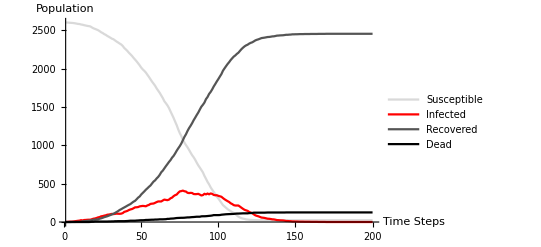

2578

125

```mathematica
dim = 51;
init = Table[0, {dim}, {dim}];
init[[26,26]] = 1;
plotList = {};
niterations = 200;
susc = {};
inf = {};
rec= {};
dead = {};
For[i= 1, i≤ niterations,
AppendTo[susc,Count[Flatten[init],0]];
AppendTo[inf, Count[Flatten[init],1]];
AppendTo[rec, Count[Flatten[init],2]];
AppendTo[dead, Count[Flatten[init],3]];
AppendTo[plotList,ArrayPlot[init,
ColorRules->{0->White, 1-> Red, 2-> Gray, 3->Black}]];
init = updSIR[init], i++];
(*Export["~/Documents/Kinesis/JohnConway/JohnConway_BasicModel.gif",plotList]*)
ListAnimate[plotList]
ListPlot[{susc,inf,rec, dead},
PlotStyle->{LightGray, Red, Darker[Gray],Black},
PlotLegends -> {"Susceptible","Infected","Recovered","Dead"},
PlotRange->{{1,niterations},{0,2601}},
Joined->True,
AxesLabel->{"Time Steps","Population"}]
(* Total number of infections *)
rec[[niterations]] + dead[[niterations]]
(* Total number of fatalities *)
dead[[niterations]]
```

### 2. The Basic Model with Loss of Immunity

- Probability of immunity loss given removal is 0.02 (i.e. immunity lasts 50 days on average).

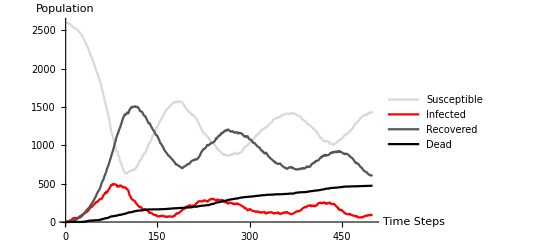

473

```mathematica
dim = 51;
init = Table[0, {dim}, {dim}];
init[[26,26]] = 1;
plotList = {};
niterations = 500;
susc = {};
inf = {};
rec= {};
dead = {};
For[i= 1, i≤ niterations,
AppendTo[susc,Count[Flatten[init],0]];
AppendTo[inf, Count[Flatten[init],1]];
AppendTo[rec, Count[Flatten[init],2]];
AppendTo[dead, Count[Flatten[init],3]];
AppendTo[plotList,ArrayPlot[init,
ColorRules->{0->White, 1-> Red, 2-> Gray, 3->Black}]];
init = updLossOfImmunity[init], i++];
(*Export["~/Documents/Kinesis/JohnConway/JohnConway_LossOfImmunity.gif",plotList]*)
ListAnimate[plotList]
ListPlot[{susc,inf,rec, dead},
PlotStyle->{LightGray, Red, Darker[Gray],Black},
PlotLegends -> {"Susceptible","Infected","Recovered","Dead"},
PlotRange->{{1,niterations},{0,2601}},
Joined->True,
AxesLabel->{"Time Steps","Population"}]
(* Total number of fatalities *)
dead[[niterations]]
```

### 3. The Basic Model with an Initial Partially Vaccinated Population

- Probability of initial vaccination is 0.3.

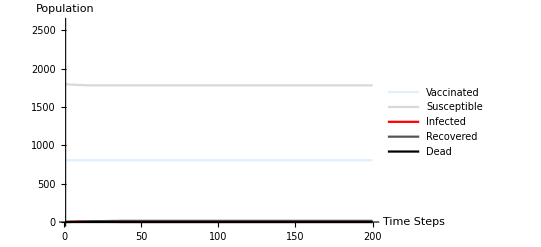

15

0

```mathematica
dim = 51;
init = Table[-RandomVariate[BernoulliDistribution[0.3]], {dim}, {dim}];
init[[26,26]] = 1;
plotList = {};
niterations = 200;
vacc = {};
susc = {};
inf = {};
rec= {};
dead = {};
For[i= 1, i≤ niterations,
AppendTo[vacc,Count[Flatten[init],-1]];
AppendTo[susc,Count[Flatten[init],0]];
AppendTo[inf, Count[Flatten[init],1]];
AppendTo[rec, Count[Flatten[init],2]];
AppendTo[dead, Count[Flatten[init],3]];
AppendTo[plotList,ArrayPlot[init,
ColorRules->{-1 -> LightBlue,0->White, 1-> Red, 2-> Gray, 3->Black}]];
init = updVaccine[init], i++];
(*Export["~/Documents/Kinesis/JohnConway/JohnConway_Vaccinations.gif",plotList]*)
ListAnimate[plotList]
ListPlot[{vacc,susc,inf,rec, dead},
PlotStyle->{LightBlue,LightGray, Red, Darker[Gray],Black},
PlotLegends -> {"Vaccinated","Susceptible","Infected","Recovered","Dead"},
PlotRange->{{1,niterations},{0,2601}},
Joined->True,
AxesLabel->{"Time Steps","Population"}]
(* Total number of infections *)
rec[[niterations]] + dead[[niterations]]
(* Total number of fatalities *)
dead[[niterations]]
```